# Multi - Scattering Crystal

```mathematica
CrystalThickness=1000; (*μm*)
path[depth_,θ_]:=(CrystalThickness - depth)/Cos[θ]
```

```mathematica
MultiData={
(* energy [MeV], thickness[μm], ΔE,Estraggling, θstraggling [mrad],Lateral spread [μm]*)
{{20,50,0.16357,0.021696,3.0681,0.015202},
{20,100,0.3284,0.030806,4.3568,0.043284},
{20,300,0.99982,0.054199,7.6748,0.23034},
{20,500,1.6917,0.071151,10.085,0.50851},
{20,700,2.4059,0.085747,12.158,0.86669},
{20,1000,3.5262,0.10582,14.973,1.5513},
{20,1500,5.5524,0.13882,19.407,3.1579}
},
{{50,50,0.077627,0.021721,1.2418,0.0061349},
{50, 100,0.15537,0.030741,1.7576,0.017375},
{50,300,0.46743,0.053399,3.0535,0.090756},
{50,500,0.78128,0.069138,3.9542,0.19628},
{50,700,1.0969,0.082045,4.6933,0.32679},
{50,1000,1.5737,0.098494,5.636,0.56215},
{50,1500,2.3772,0.12153,6.9582,1.0434}
},
{{80,50,0.053681,0.021993,0.78711,0.0038867},
{80,100,0.10739,0.031112,1.1135,0.011},
{80,300,0.32257,0.053951,1.9311,0.057284},
{80,500,0.53826,0.069733,2.4963,0.12353},
{80,700,0.75446,0.082607,2.9576,0.20509},
{80,1000,1.0797,0.09891,3.5419,0.35134},
{80,1500,1.6245,0.1215,4.3523,0.64897}
},
{{100,50,0.045373,0.022216,0.63548,0.0031417},
{100, 100,0.090763,0.031424,0.89891,0.0088893},
{100,300,0.2725,0.054469,1.5583,0.046256},
{100,500,0.45451,0.070371,2.0135,0.099668},
{100,700,0.63679,0.083326,2.3845,0.16533},
{100,1000,0.91074,0.099704,2.8538,0.2829},
{100,1500,1.3687,0.12234,3.5028,0.52153}
},
{{120,50,0.039681,0.022452,0.53433,0.0026431},
{120,100,0.079372,0.031756,0.75578,0.0074776},
{120,300,0.23824,0.05503,1.3099,0.038893},
{120,500,0.39728,0.071079,1.6921,0.083768},
{120,700,0.55648,0.084144,2.0034,0.1389},
{120,1000,0.7956,0.10065,2.3752,1.6274},
{120,1500,1.195,0.12342,2.9401,0.43741}
},
{{150,50,0.033866,0.022803,0.43305,0.0021429},
{150,100,0.067738,0.03225,0.61249,0.006062},
{150,300,0.20328,0.055876,1.0613,0.031519},
{150,500,0.33892,0.072158,1.3707,0.0067863},
{150,700,0.47465,0.085404,1.6226,0.11249},
{150,1000,0.67841,0.10212,1.9406,0.19225},
{150,1500,1.0185,0.12517,2.3792,0.35376}
},
{{170,50,0.03108,0.023042,0.38531,0.0019069},
{170,100,0.062163,0.032588,0.54496,0.0053942},
{170,300,0.18654,0.056457,0.94422,0.028044},
{170,500,0.31098,0.072902,1.2194,0.060371},
{170,700,0.43548,0.086279,1.4433,0.10006},
{170,1000,0.62237,0.10316,1.726,0.17097},
{170,1500,0.93416,0.12642,2.1157,0.3145}
},
{{200,50,0.027908,0.023394,0.33151,0.0016408},
{200,100,0.055819,0.033086,0.46886,0.0046414},
{200,300,0.16749,0.057316,0.8123,0.024126},
{200,500,0.2792,0.074006,1.0489,0.051931},
{200,700,0.39095,0.087579,1.2414,0.086057},
{200,1000,0.55866,0.1047,1.4844,0.14702},
{200,1500,0.83839,0.12829,1.8192,0.27036}
},
{{230,50,0.025529,0.02374,0.29165,0.0014427},
{230,100,0.051061,0.033575,0.41248,0.004081},
{230,300,0.15321,0.058161,0.71458,0.021212},
{230,500,0.25538,0.075095,0.9227,0.0045656},
{230,700,0.35759,0.088865,1.092,0.075653},
{230,1000,0.51095,0.10623,1.3056,0.12924},
{230,1500,0.76672,0.13015,1.5998,0.23761}
},
{{260,50,0.0237,0.024114,0.26091,0.0012909},
{260,100,0.047401,0.034103,0.36899,0.0036515},
{260,300,0.14222,0.059074,0.63922,0.018979},
{260,500,0.23706,0.076272,0.82536,0.040846},
{260,700,0.33192,0.090254,0.97674,0.067678},
{260,1000,0.47426,0.10789,1.1677,0.1156},
{260,1500,0.7116,0.13217,1.4307,0.21251}
}
};
Dimensions[MultiData]
```

{10,7,6}

```mathematica
ΔE=Interpolation[Flatten[MultiData[[1;;10,1;;7,{1,2,3}]],1]];
Estr=Interpolation[Flatten[MultiData[[1;;10,1;;7,{1,2,4}]],1]];
θstr=Interpolation[Flatten[MultiData[[1;;10,1;;7,{1,2,5}]],1]];
```

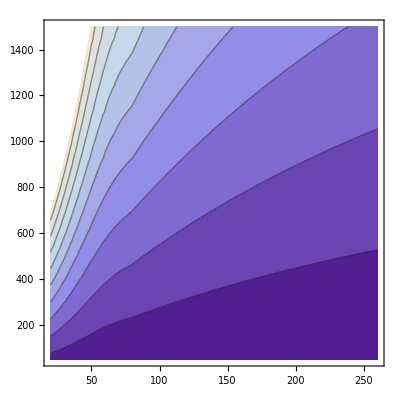

```mathematica
ContourPlot[ΔE[x,y],{x,20,260},{y,50,1500}]
```

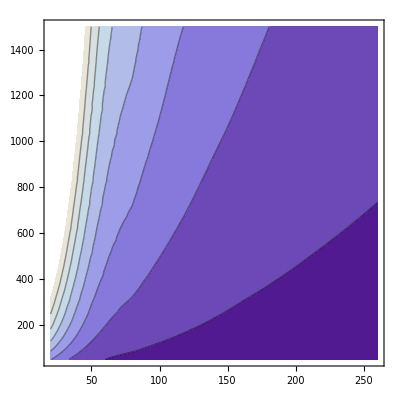

```mathematica
ContourPlot[θstr[x,y],{x,20,260},{y,50,1500}]
```

## Elastics Scattering

```mathematica
m=938.27203;
```

```mathematica
Pa[T_,α_]:={1/2 (2 m+T+T Cos[α]),√(T (2 m+T)) Cos[α/2]^2,(√(m T) Sin[α])/(√2)}
Pb[T_,α_]:={1/2 (2 m+T-T Cos[α]),√(T (2 m+T)) Sin[α/2]^2,-(√(m T) Sin[α])/(√2)}
```

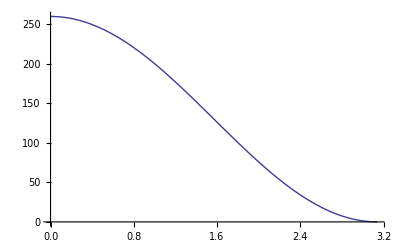

```mathematica
Plot[260(1+Cos[α])/2,{α,0,π}]
```

### Monte Carlo

```mathematica
Angle[A_]:=ArcTan[A[[2]],A[[3]]]
TKE[A_]:=A[[1]]-m
Scattered[A_,path_]:=Module[{newE,newk,oldθ,newθ},
If[(260≥ A[[1]]-m≥ 20 )&&(1500≥ path≥50),
newE=A[[1]]-RandomVariate[NormalDistribution[ΔE[A[[1]]-m,path],Estr[A[[1]]-m,path]]];
newk=√(newE^2-m^2);
oldθ=ArcTan[A[[2]],A[[3]]];
newθ=RandomVariate[NormalDistribution[oldθ,θstr[A[[1]]-m,path]/1000]];
{newE,newk Cos[newθ],newk Sin[newθ] },
{0,1,0}]
]
```

```mathematica
n=10000;
θNNList=Table[ArcCos[2RandomReal[{0.3,0.7}]-1],{i,1,n}];
Tin=260;
RecoilList=Table[{
Pa[Tin,θNNList[[i]]],Angle[Pa[Tin,θNNList[[i]]]],
Pb[Tin,θNNList[[i]]],Angle[Pb[Tin,θNNList[[i]]]]
},{i,1,n}];
DepthList=Table[RandomReal[{0,950}],{i,1,n}];
```

```mathematica
RecoilList[[1,1]]
e=RecoilList[[1,1,1]]-m
{RecoilList[[1,2]],RecoilList[[1,4]]}
DepthList[[1]]
l=path[DepthList[[1]],RecoilList[[1,2]]]
{ΔE[e,l],Estr[e,l],θstr[e,l]}
```

{991.538,152.693,281.919}

53.266

{1.07441,-0.444028}

909.24

190.57

{0.278566,0.0431251,2.27625}

```mathematica
Scattered[RecoilList[[1,1]],path[DepthList[[1]],RecoilList[[1,2]]]]
```

{991.332,151.417,281.881}

```mathematica
MSData=Table[
{Scattered[RecoilList[[i,1]],path[DepthList[[i]],RecoilList[[i,2]]]],
Scattered[RecoilList[[i,3]],path[DepthList[[i]],RecoilList[[i,4]]]]
},{i,1,n}];
```

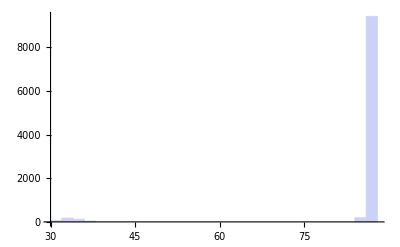

```mathematica
Histogram[
Table[(Angle[MSData[[i,1]]]-Angle[MSData[[i,2]]])180/π,{i,1,n}]
]
```

```mathematica
Length[Select[Table[(Angle[MSData[[i,1]]]-Angle[MSData[[i,2]]])180/π,{i,1,n}],#>80&]]
```

9606

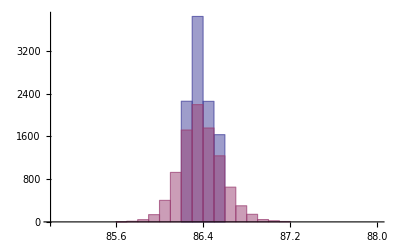

```mathematica
Histogram[{
Table[(RecoilList[[i,2]]-RecoilList[[i,4]])180/π,{i,1,n}],
Table[(Angle[MSData[[i,1]]]-Angle[MSData[[i,2]]])180/π,{i,1,n}]
},{85,88,0.1}]
```

```mathematica
0.8/180 π 1000//N
```

13.9626

```mathematica
√(17.5^2-10.5^2)
```

14.

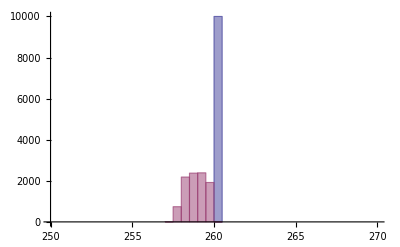

```mathematica
Histogram[{
Table[TKE[RecoilList[[i,1]]]+TKE[RecoilList[[i,3]]],{i,1,n}],
Table[TKE[MSData[[i,1]]]+TKE[MSData[[i,2]]],{i,1,n}]
},{250,270,0.5}]
```